```mathematica
RandomSample[Join[Range[-10,10]3,
Range[-10,10]3+165]]
```

```mathematica
1/((.259*29.9)/(.6172*11.667)-1)
```

13.2557

```mathematica
1/(1-Exp[-])
```

```mathematica
.26 30/(.6 13.5)
```

0.962963

```mathematica
RandomSample[Join[Range[-10,10]3,
Range[-10,10]3+165]]
```

```mathematica
quadratic part of fit Ω^2 t^2 of RSB vs BSB
ratio should give n/(n+1)
calibrate height against carrier?


carrier dephasing only quadratically sensitive to temp?
```

```mathematica
h=6.62607004 10^-34;
kHz=10^3;
uK=10^-6;
kB=1.38064852 10^-23;
1/(Exp[(h 140 kHz)/(kB 15uK)]-1)
```

1.7697

```mathematica
1/(Exp[(h 166/2 kHz)/(kB 12.5uK)]-1)
```

2.66455

```mathematica
1/(.54 15/(.28 27)-1)
```

14.

```mathematica
Ωn=
```

```mathematica
Sum[Pn/2(1-Cos[Ωn t]),{n,4}]
```

```mathematica
nbar=1/(Exp[(h (f02-f0)/2 kHz)/(kB T uK)]-1);
fit={f02->168.45,f0->.852,T->12.5};

nbar/.fit

√((D[nbar, f02])^2 sf02^2+(D[nbar, f0])^2 sf0^2+(D[nbar, T])^2 sT^2)/.{sf02->1.12,sf0->.432,sT->1.56}/.fit
```

2.63489

0.385198

```mathematica
Integrate[Exp[-n/nn]/nn,{n,0,Infinity}]
```

ConditionalExpression[1,Re[1/nn]>0]

```mathematica
us=10^-6;
Subscript[ΩLDR, BSB]=(2π)/(2 116us)
```

(250000 π)/29

```mathematica
.5/((ηR ΩR √(nbar+1))/(2π))/us
```

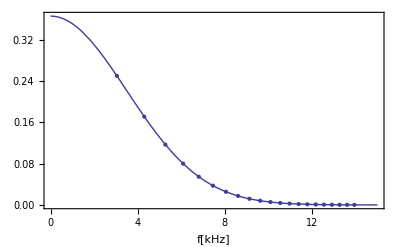

4.93371

{-50,-40,-30,-20,-10,0,10,20,30,40,50,60,70,80,90,100,110,120}

```mathematica
Clear["Global`*"]
kHz=10^3;us=10^-6;amu=1.660539040 10^-27;ℏ=(6.62607004 10^-34)/(2π);nm=10^-9;m=133amu;ωrad=2π(168.45-.852)/2 kHz;λR=852 nm;x0=√(ℏ/(2 m ωrad));ΔkR=√2(2π)/λR;ηR=x0 ΔkR;ΩR=(2π)/(2 36.5us);nbar=2.63;
Ωn=ηR ΩR √(n+1);
Pn=Exp[-n/nbar];

data=Table[{Ωn/(2π kHz),1/2 Pn/2},{n,0,20}];
fitfn=A Exp[-(f/Γ)^2];

fit=FindFit[
data,
fitfn,
{A, Γ},f
];

Show[
{
Plot[fitfn/.fit,{f,0,15},Axes->False,Frame->True,FrameLabel->{"f[kHz]",""}] ,
ListPlot[data]
}
]
Γ/.fit
```

```mathematica
a
```